Quantum Linear System Problems with QSP |

Function Approximationpaclet:QuantumMob/Q3S/tutorial/QuantumLinearSystemProblems#1625771319 | A QSP representationpaclet:QuantumMob/Q3S/tutorial/QuantumLinearSystemProblems#1829545107
Polynomial Approximationpaclet:QuantumMob/Q3S/tutorial/QuantumLinearSystemProblems#434079351 |

Based on a QSPPACK documenthttps://qsppack.gitbook.io/qsppack/examples/quantum-linear-system-problems

The quantum linear system problem (QLSP) is a quantum variant of the linear system problem

Ax=b

Given the access to an invertible matrix A and to a normalized quantum state b, QLSP asks a construction of the solution quantum state

x:=A^-1 b / (‖A^-1 b‖)_2

with bounded error.

Suppose the condition number of the coefficient matrix is κ:=(‖A‖)_2(‖A^-1‖)_2 and A∈ℂ^(N×N). Recently, some near-optimal quantum algorithms have been suggested for solving QLSP with bounded error ϵ and complexity 𝒪(κlog(1/ϵ)polylog(N)).

This example provides a much simpler construction of the solution to QLSP.

QSPpaclet:QuantumMob/Q3S/ref/QSPQuantumMob Package Symbol | Represents a quantum signal processing, a unitary representation of polynomial
QSPFindpaclet:QuantumMob/Q3S/ref/QSPFindQuantumMob Package Symbol | Finds a quantum singal processing representing a target polynomial
ChebyshevApproximationpaclet:QuantumMob/Q3S/ref/ChebyshevApproximationQuantumMob Package Symbol | Finds a Chebyshev expansion coefficients that approximate a target function
ChebyshevCoefficientspaclet:QuantumMob/Q3S/ref/ChebyshevCoefficientsQuantumMob Package Symbol | Gives a list of Chebyshev expansion coefficients of a polynomial
ChebyshevSeriespaclet:QuantumMob/Q3S/ref/ChebyshevSeriesQuantumMob Package Symbol | Represents a Chebyshev expansion of a polynomial

Functions useful for the quantum signal processing (QSP) approach to quantum linear system problems (QLSP).

Make sure to load the Q3 framework.

```mathematica
Needs["QuamtumMob`Q3`"]
```

Function Approximation

An idea for solving QLSP is approximately implementing the map A↦A^-1. Hence, in light of quantum signal processing (QSP), the implementation boils down to a scalar function f(x)=x^-1. Without loss of generality, the matrix is assumed to be normalized so that (‖A‖)_2≤1. Then, the condition number implies that the eigenvalues of A lie in the interval D_κ:=[-1,-1/κ]∪[1/κ,1]. Hence, we restrict f(x) to the interval D_k. This restriction is necessary to exclude the singularity of f(x) at x=0.

Set the (maximum) condition number of matrices of our concern.

```mathematica
$κ=10
```

10

Scale down the target function by a factor of 1/2κ so that

```mathematica
target[x_]:=1/(2*$κ*x)
```

This improves the numerical stability.

Set the interval in accordance with the condition number.

```mathematica
$interval=Interval[{-1,-1/$κ},{1/$κ,1}]
```

Interval[{-1,-1/10},{1/10,1}]

The target function looks as follows.

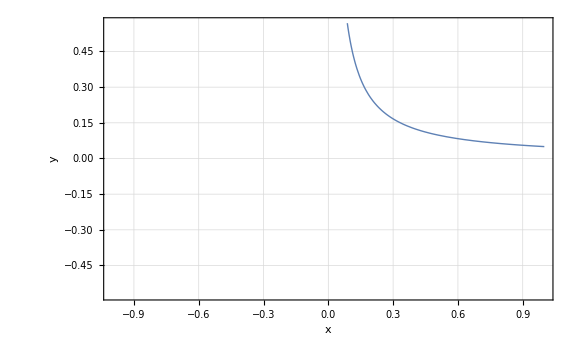

```mathematica
Plot[target[x],{x,-1,1},
FrameLabel->{"x","y"}]
```

Polynomial Approximation

Let us now find a polynomial approximation to f(x). We note that f(x) is odd, and hence we need to find an odd polynomial approximation to f(x) on the interval D_κ.

Make sure to load Q3.

```mathematica
Needs["QuamtumMob`Q3`"]
```

Set the degree of the approximate polynomial. Note that d=2n+(1-p)/2.

```mathematica
$n=25
$degree=51
```

25

51

Find a polynomial approximation of degree d.

```mathematica
fun=ChebyshevApproximation[target,{$n,-1},$interval,
"Parity"->True,
"Points"->120]
```

ChebyshevSeries[…]

Compare the target function and the approximate polynomial.

```mathematica
Plot[{target[x],fun[x]},{x,-1,1},
PlotLegends->{"target","approx."},
FrameLabel->{"x","y"}]
```

-Graphics-

Plot the approximation error.

```mathematica
Plot[Abs[target[x]-fun[x]],{x,1/$κ,1},
PlotRange->{0,0.01},
PlotLegends->{"target","approx."},
FrameLabel->{"x","δy"}]
```

-Graphics-

A QSP representation

Finally, we find a QSP representation of the polynomial approximation.

Make sure to load Q3.

```mathematica
Needs["QuamtumMob`Q3`"]
```

Find a QSP representation.

```mathematica
qsp=QSPFind[fun]
```

QSP[…]

Compare the target function, the approximate polynomial, and the QSP representation.

```mathematica
Plot[{target[x],fun[x],qsp[x]},{x,-1,1},
PlotStyle->{Thick,Thick,{Thick,Dashed}},
PlotLegends->{"target","approx.","QSP"},
FrameLabel->{"x","y"}]
```

-Graphics-

Plot the residual error.

```mathematica
Plot[Abs[fun[x]-qsp[x]],{x,1/$κ,1},
PlotRange->All,
PlotLegends->{"target","approx."},
FrameLabel->{"x","δy"}]
```

-Graphics-

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems
▪Q3: Symbolic Quantum Simulation

| Related Tech Notes
▪Quantum Linear System Problems
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3

| Related Links
 ▪QSPPACKhttps://github.com/qsppack/QSPPACK by Y. Dong, J. Wang, X. Meng, H. Ni and L. Lin.
▪Y. Dong et al. (2021)https://doi.org/10.1103/PhysRevA.103.042419, Physical Review A 103, 042419 (2021), ".Efficient phase-factor evaluation in quantum signal processing."
▪J. Wang et al. (2022)https://doi.org/10.22331/q-2022-11-03-850, Quantum 6, 850 (2022), "On the energy landscape of symmetric quantum signal processing."
▪L. Lin (2022)https://arxiv.org/abs/2201.08309, arXiv:2201.08309,  "Lecture Notes on Quantum Algorithms for Scientific Computation."
▪A. Gilyen, Y. Su, G. Hao, and N. Wiebe (2019)https://doi.org/10.1145/3313276.3316366, Proceedings of the 51st Annual ACM SIGACT Symposium on Theory of Computing, "Quantum singular value transformation and beyond: exponential improvements for quantum matrix arithmetics."
▪J. Haah (2019)https://doi.org/10.22331/q-2019-10-07-190, Quantum 3, 190 (2019), "Product Decomposition of Periodic Functions in Quantum Signal Processing."
▪C. T. Kelley (1999)https://doi.org/10.1137/1.9781611970920, Iterative Methods for Optimization (SIAM, 1999).
▪W. Sun and Y.-X. Yuan (2006)https://doi.org/10.1007/b106451, Optimization Theory and Methods (Kluwer Academic Publishers, 2006).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
▪About Q3